# Physics 230 -- Lab 2 (Lists and Functions)

## Branton J. Campbell, BYU Physics & Astronomy R. Steven Turley, BYU Physics and Astronomy

## Introduction (15 min)

### Lists (5 min)

#### Introduction

In physics it is natural to organize data and numbers in lists and tables.  One example would be the elements of a vector.  Another might be a list of voltages in a circuit at different times, the speed of a swinging penculum at different angles, or the length of a rod at different temperatures.  Experimental data is often a list of characteristics of a system as a function of different measurements parameters.  The basic mechanism for storing collections of numbers of other things in Mathematica is the List.  It is a fundamental and central idea in Mathematica and an important concept in computational physics in general.

If you have had previous programming experience using other languages, you’ll recognize that a Mathematica List is similar to an array in other programming languages.

In the following sections we’ll introduce how Mathematica Lists can be used to represent the various kinds of data you might work when using Mathematica to solve physics problems.

#### Vectors

Geometrically, a vector is a quantity that has a magnitude and a direction associated with it.  Common vectors you have seen so far in physics include position, velocity, acceleration, force, angular momentum, and torque.  A vector can be expressed in terms of its components in different directions.  For example, in rectangular (Carteisian) coordinates, a two dimensional position can be represented in terms of its x position (the distance along the x axis) and its y position (the distance along the y axis).  For example, the vector w in the following figure has an x component w_x and a y component w_y.

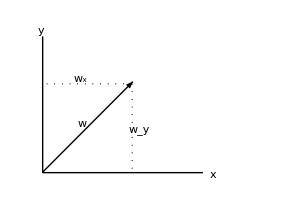

We write this mathematically as a row vector (w_x,w_y) or a column vector (w_x
w_y).  In Mathematica, we store the elements in curly brackets.

```mathematica
w={wx,wy}
```

A three dimensional vector is represented by its components in the x, y, and z directions.

```mathematica
w={wx, wy, wz}
```

Vectors are sometimes more conveniently represented in other coordinate systems than rectangular coordinate systems.  For instance, in Physics 121 you learned that two-dimensional rotational motion is most conveniently represented in the polar coordinates r and θ as shown in the figure below.

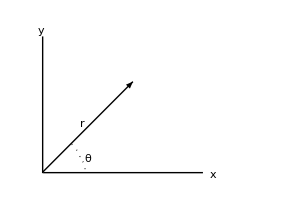

The component r is the length of the vector and the component θ is the angle the vector makes with the x axis.  It could be stored in Mathematica as

```mathematica
w={r, theta}
```

We’ll see in a later lesson that Mathematica has functions to do many useful things with vectors like adding and subtracting them, converting from one coordinate system to another, finding cross products and dot products, and drawing them.

#### Other Lists

You can also create general lists of numbers in Mathematica using the same notation you did with vectors.  For example, let’s say you computed or measured the temperature of a rod cooling down in time to have the values in the following table.
time (min) | temperature (K)
0 | 400
1 | 350
2 | 306
3 | 268
4 | 235
5 | 205
6 | 180
7 | 157
8 | 138
9 | 120
10 | 105
11 | 92
You could work with this in Mathematica as a list of lists which you would enter as follows.

```mathematica
temp={{0,400},{1,350},{2,306},{3,268},{4,235}, {5,205},{6,180},{7,157},{8,138},{9,120},{10,105},{11,92}}
```

{{0,400},{1,350},{2,306},{3,268},{4,235},{5,205},{6,180},{7,157},{8,138},{9,120},{10,105},{11,92}}

Once you had stored the data in a list like this you could manipulate it, find the best equation to describe its functional form, plot it, or transform it in other ways.  We’ll see how to do this in future lessons.

As you’ll see later, Mathematica has a built-in functions to do many powerful things with lists of numbers, symbols, and strings.

### Functions (10 min)

In physics you will frequently have occasions to perform the same calculation over and over.  In these cases, you can save a lot of time by saving the steps to do the calculation as a function.  A function can have arguments, variables used in the function to determine its value.  As an example, let’s say you wanted to find the position of a simple harmonic oscillator with amplitude 10, a frequency of 5 Hz and a phase of 0 at various times.  You could create the function sho as follows.

```mathematica
sho[t_]:=10 Cos[2 Pi 5 t]
```

The underbar after the t in the function defintion identifies it as a variable which will be substituted into the function.  The variable t is what is known as a dummy variable.  It won’t replace values of t defined outside the function and its definition won’t persist beyond the execution of the function. 

Now that the function is defined, you could compute its values as various times.

```mathematica
sho[1.724]
sho[3.619]
sho[s]
```

-7.28969

8.27081

10 cos(10 π s)

You could also use this function as an argument to other functions.  If you wanted to plot the amplitude of sho as a funciton of time, you could do it as follows.

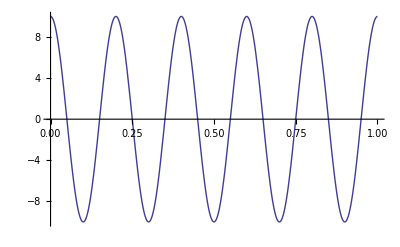

```mathematica
Plot[sho[t],{t,0,1}]
```

Functions can have any number of arguments, including no arguments.

Create a funciton which will use the Ideal Gas Law, pV=Nk_BT to compute the pressure of an ideal gas at various absolute temperatures.  Use V = 0.05 m^3, N=1.5×10^22 molecules, k_B is 1.38× 10^-23 J/K.  Use this function to compute the pressure of this gas at 200 K, 300 K, and 400 K.

```mathematica
pressure [v_,n_,k_,T_]=(n*k*T)/v;
v = 0.05;
n = 1.5 * 10^22;
k = 1.38 * 10^-23;
pressure[v,n,k,200]
pressure[v,n,k,300]
pressure[v,n,k,400]
```

828.

1242.

1656.

Your functions can be more complex than what you can express in a single line.  This is accomplished by using the Module statement.  A Module has two arguments.  The first argument is a list of variables which are used inside your function, but you don’t want to use outside your function.  The second argument is a sequence of statements terminated by semicolons which make up the body of your function.

As an example, suppose you wanted to write a function to compute where the image from a compound lens would be.  For each element, the location of the image can be computed from the equation 1/f=1/o+1/i.  Solving for i, 1/i=1/f-1/o, i=1/(1/f-1/o).  For the next element, the image of the previous element becomes the object of previous element.  Using some specific focal lengths,

```mathematica
image[object_]:=Module[{f1=2, f2=-3, f3=2.7, f4=-4.6, f5=10, i1, i2, i3, i4},
i1=1/(1/f1-1/object);
i2=1/(1/f2-1/i1);
i3=1/(1/f3-1/i2);
i4=1/(1/f4-1/i3);
1/(1/f5-1/i4)
]
image[11]
```

0.69921

Notice that the last statement of the Module doesn’t have a semicolon at the end.  In this case, the function will return the value computated in this last statement.  Also note that the variables in the first argument of Module can either be initialized there, or computed later in the Module.

## Working with functions (15 min)

### (#1) Pure (argumentative) functions (5 min)

The "arguments" of a function are the variables that the function takes as input.  For f(x), we say that f is the function and x  is its argument.  To train a function to take an argument, we use what we call a variable "pattern" (e.g. a variable name followed by an underscore).  Once we have trained a function to take an argument, we can call it an "argumentative" function.  Mathematica's documentation refers to it as a  Pure Function.  Remember this terminology -- it will be helpful in later labs.

(a) Evaluate the following three cells and observe each output carefully.

```mathematica
f[x] = 3 x ; (* without pattern *)
g[x_] = 3 x ; (* with pattern *)
```

```mathematica
f[x]
g[x]
```

3 x

3 x

```mathematica
f[y]
g[y]
```

f(y)

3 y

When x is used as the argument, functions f and g both know what to do because x was an explicit part of the definition.  But only g seems to know what to do with y, which wasn't explicity defined.  The unusual quantity "x_" in the left-hand-side of the definition of g, is called a pattern, and essentially means "an arbitrary quantity called x".  Its effect is such that an any argument sent to g simply replaces x on the right-hand side of its definition.  This is the way that we expect functions to behave.

Clear all variables before continuing.

```mathematica
Clear["`*"]
```

(b) When defining functions, it is often helpful to employ the delayed assignment (SetDelayed), indicated by ":=" rather than "=".  Delayed assignments allow you to safely retrieve the current values of any global variables that you use in your function definition (otherwise you get stuck with the value that was current when you defined the function).  Evaluate the cells below.  Explain the effect of the delayed assignment to your instructor or TA.

```mathematica
m = 2;
f[x_] = m x ; (* regular assignment *)
g[x_] := m x ; (* delayed assignment *)

f[7]
g[7]
```

14

14

```mathematica
m = 3;
f[7]
g[7]
```

14

21

(c) In the cell below, use a delayed assignment and a variable "pattern" to define an argumentative function, h(x) = x^2- m.  Then set the value of m to 1 and demonstrate that your function properly evaluates h(1), h(2) and h(3).

```mathematica
h[x_] := x^2 - m;
m=1;
h[1]
h[2]
h[3]
```

0

3

8

### (#2) Prefix and Postfix functional forms (10 min)

(a) In addition to the standard g[x] form for calling a function, Mathematica provides several different shorthand forms for calling functions.  We emphasize two such forms here: Prefix (@) and Postfix (//), each of which are very convenient when used properly.  Evaluate the following two cells and think carefully about the output.

```mathematica
g[x]     (* function call in standard notation *)
g@x      (* equivalent shorthand call in "prefix" notation *)
x//g  (* equivalent shorthand call in "postfix" notation *)
```

x

x

x

The postfix notation is like reverse polish notation if you have ever used an HP calculator.  Try these examples and explain the output to your TA.

```mathematica
(* the sequential approach *)
7/3
N[%]
Round[%]
Exp[%]
Log[%]
```

7/3

2.33333

2

ⅇ^2

2

```mathematica
Log[Exp[Round[N[7/3]]]]  (* standard form *)
7/3 // N // Round // Exp // Log  (* postfix form *)
```

2

2

(b) Because Cos and ArcCos are inverse functions, arccos(cos(x)) evaluates to x.  In the cell below, evaluate the arccos(cos(π)) using the prefix notation for Cos and the postfix notation for ArcCos.  The Mathematica symbol for π is Pi., which is one of several built-in Mathematical Constants.

```mathematica
Cos[π//ArcCos]
Cos@π//ArcCos
```

π

π

(c) In the cell below, create the 2x2 matrix, {{1, 1}, {-1, 1}},  and then apply a succession of functions in postfix notation to invert it, transpose it, evaluate its determinant, and convert the result to a numeric floating-point value.  Do all this on one line with a single expression.

```mathematica
({{1, 1}, {-1, 1}})//Inverse//Transpose//Det
```

1/2

## Working with lists (70 min)

### (#3) Generating lists (10 min)

Go to the DC guide page on List Manipulation and review the "Basic Examples" for simple list functions like Table, Array, Range, Join, Append, Reverse, Sort, Transpose, Flatten, Union, and for each of the functions in the "Elements of Lists" section.

(a) The use of curly brackets is really a shorthand notation for the List function.  Try the following.

```mathematica
{a,b,c}             (* shorthand notation *)
List[a,b,c]    (* standard notation *)
% // FullForm  (* coverts shorthand notation into standard notation *)
```

{a,b,c}

{a,b,c}

List[a,b,c]

(b) Lists are fundamental to the way that Mathematica operates, and there are many ways to generate them.  Here are a few equivalent ways to create a list of integers from 1 to 10.  Any one of them might be appropriate depending on the circumstances.  Go to the DC guide page on Constructing Lists, and browse the basic examples associated with each of these functions.  Give special attention to the Range and Table functions.

```mathematica
{1,2,3,4,5,6,7,8,9,10}
List[1,2,3,4,5,6,7,8,9,10]
Table[n^2,{n,1,10}]
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

{1,4,9,16,25,36,49,64,81,100}

{1,2,3,4,5,6,7,8,9,10}

(c) In the cell below, use two different methods (Range and Table) to create a list of the even numbers from 0 to 100.

```mathematica
Range[0,100,2]
Table[n,{n,0,100,2}]
```

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

### (#4) Properties of lists (10 min)

(a) Lists have a variety of properties that can be measured or tested.  In the cell below, create a list called temp containing at least five distinct numerical values.  Then measure the Length, the Maximum value and the Minimum value of your list.

```mathematica
temp = {1,4,6,8,4,8,3,23};
Length[temp]
Max[temp]
Min[temp]
```

8

23

1

(b) As mentioned earlier, matrices and vectors are represented in Mathematica as lists.  A vector is a one-dimensional list, whereas a matrix is a two-dimensional nested list (i.e. a list of lists).  Higher-dimensional nested lists are also very common.  We say that nested lists have more than one "level" -- the top level is level 1, the next level is level 2, and so on.  The Dimensions function shows how many levels a list has and how many list elements exist at each level.  Try the following examples and explain the output to your TA.

```mathematica
{1,2,3}//Dimensions
```

{3}

```mathematica
{{1,2,3},{4,5,6}}//Dimensions
```

{2,3}

```mathematica
{{9,8},{7,6},{5,4}} //  Dimensions
```

{3,2}

```mathematica
{17} // Dimensions
```

{1}

```mathematica
8// Dimensions
```

{}

```mathematica
{} // Dimensions
```

{0}

```mathematica
{{{9,8,7,6,5},{5,6,7,8,9}},{{1,2,3,4,5},{5,4,3,2,1}}} //  Dimensions
```

{2,2,5}

### (#5) Parts of lists (10 min)

One can reach inside any list, even a nested list, to extract one or more elements by specifying their locations.  Browse the DC guide page on Elements of Lists and review the basic examples for Part.

(a) Evaluate the following examples and explain the output.

```mathematica
temp = Table[12*(i-1) + 4*(j-1)+k,{i,2},{j,3},{k,4}]
temp[[1]]
temp[[2,2]]
temp[[2,3,4]]
temp[[1,1,2;;4]]
```

({1,2,3,4} | {5,6,7,8} | {9,10,11,12}
{13,14,15,16} | {17,18,19,20} | {21,22,23,24})

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12)

{17,18,19,20}

24

{2,3,4}

(b) In the cell below, demonstrate an application of each of the following functions: First,  Last,  Rest,  Most,  Take, Drop and the shorthand form of Part to the list of integers from 1 to 10.

```mathematica
zeroToTen = Range[10];
First[zeroToTen]
Last[zeroToTen]
Rest[zeroToTen]
Most[zeroToTen]
Take[zeroToTen,4]
Take[zeroToTen,-4]
Drop[zeroToTen,{1,7,2}]
```

1

10

{2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9}

{1,2,3,4}

{7,8,9,10}

{2,4,6,8,9,10}

### (#6) Searching Lists (5 min)

Review the functions presented on the tutorial page about Testing And Searching List Elements.

(a) In the cell below, we use Position to locate the number 9 in a ragged nested list, and Count the number of times that the number 9 appears in the list.  Evaluate the cell and explain the output.

```mathematica
temp = {9,{8,9,5},6,{3,{8,2,{9,5}}}};
Position[temp,9]
Count[temp,9,∞]
```

{{1},{2,2},{4,2,3,1}}

3

(b) One can also Select list elements that satisfy a certain test.  For example, given the numbers from 1 to 20, we can extract the following sublists.

```mathematica
temp = Range[20]
Select[temp,OddQ]  (* odd *)
Select[temp,#>10&]  (* greater than 10 *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{1,3,5,7,9,11,13,15,17,19}

{11,12,13,14,15,16,17,18,19,20}

(c) In the cell below, use Select to obtain a list of all of the prime numbers in the range from 1 to 100.

```mathematica
temp = Range[100];
Select[temp, PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

There are several other ways to select list elements -- we only emphasized one here.

### (#7-#11) Manipulating and processing lists (40 min)

As a physicist, you will often be faced with collections of data from computations or measurements.  You’ll frequently want to extract certain elements or list of elements from the data.  You may also want to transofrm the list in different ways or apply an operation to each element of the list.  In this section, you will learn some tools which are helpful in that kind of analysis.

#### (#7) Miscellaneous tools (10 min)

(a) In the cell below, complete the following sequence of operations on the list provided so that each operation acts on the result of the previous operation (%) and appears on a separate line.  (1) Flatten the list, (2) Sort in ascending order, (3) find the Union (i.e. the unique elements),  (4) use Complement to extract only those elements that are greater than 3, (5) Reverse the order.  If done correctly, this should yield {10, 9, 8, 7, 6, 4}.

```mathematica
dat ={{4,8,9,10},{8,6,7,1},{3,7,8,4},{3,1,2,8}};
Flatten[dat];
Sort[%];
Union[%];
Complement[%,Range[3]];
Reverse[%]
```

{10,9,8,7,6,4}

#### (#8) Joining lists together (5 min)

In the cell below, complete the following sequence of operations.  (a) Define dat1 = {2,3,4} and dat2 = {7,8,9}.  (b) Append a 5 at the back of dat1 and call the result dat3.  (c) Prepend a 6 at the front of dat2 and call the result dat4. (d) Join lists dat3 and dat4 and call the result dat5.

```mathematica
dat1= {2,3,4};
dat2 = {7,8,9};
dat3 = Append[dat1,5];
dat4 = Prepend[dat2,6];
dat5 = dat3 ~Join~dat4 (*or I could have done Join[dat3, dat4]*)
```

{2,3,4,5,6,7,8,9}

#### (#9) Map (10 min)

(a) Evaluate the cell below to send a simple list as an argument to an arbitrary function "f ".  In general, an arbitrary function won't know how to eat a list.

```mathematica
temp = {{1,2,3},{4,5,6}}
f[temp]
```

(1 | 2 | 3
4 | 5 | 6)

f((1 | 2 | 3
4 | 5 | 6))

(b) Suppose that you want to apply the function to each element of the list individually.  We can say that we want to Map the function onto each element of the list.  Evaluate the cell below to map the function f onto each element of temp.  Then browse and execute several of the basic DC examples on the Map reference page.

```mathematica
Map[f,temp]  (* standard form of the Map command *)
```

{f({1,2,3}),f({4,5,6})}

(c) Rather than mapping a function onto the level 1 (default) elements of a list, we can specify a lower level.  Evaluate the cell below, and explain to your TA how mapping at level 2 is different from the mapping at level 1.

```mathematica
Map[f, temp,{2}] (* map to level 2 *)
```

(f(1) | f(2) | f(3)
f(4) | f(5) | f(6))

(d) Use MapAt to map the function f onto the number 5 inside of temp, but nowhere else.

```mathematica
MapAt[f,temp,{2,2}]
```

(1 | 2 | 3
4 | f(5) | 6)

(e) In the cell below, use the standard form of Map to map a nameless function onto the list of integers from 1 to 10, thereby obtaining the square of each integer.  Then repeat the exercise using the shorthand "/@" form of Map.

```mathematica
myList = Range[10];
Map[Function[x,x^2],myList]
Function[x, x^2]/@ myList
```

{1,4,9,16,25,36,49,64,81,100}

{1,4,9,16,25,36,49,64,81,100}

#### (#10) Listable functions (5 min)

(a) Many mathematical functions are Listable (a.k.a. self mapping or self threading), so that they automatically get applied to each element when applied to the whole list. Here are a few examples of listable functions.  Evaluate them.

```mathematica
temp = Range[8];
temp+temp    (*  Plus is Listable  *)
10*temp        (*  Times is Listable  *)
temp^2             (*  Power is Listable  *)
Cos[temp*Pi/4] (*  Cos is Listable  *)
```

{2,4,6,8,10,12,14,16}

{10,20,30,40,50,60,70,80}

{1,4,9,16,25,36,49,64}

{1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1}

(b) Functions that are not listable must be mapped explicitly.  To see this, evaluate the following example.  You may want to review the DC reference pages for IdentityMatrix, MatrixForm and TableForm.

```mathematica
MatrixForm[IdentityMatrix[temp]]  (*  evaluation fails since these functions are not listable  *)
MatrixForm/@IdentityMatrix/@temp  (*  explicit mapping  *)
```

IdentityMatrix::dims: Dimension specification TraditionalForm`{1, 2, 3, 4, 5, 6, 7, 8} should be a positive machine integer or a pair of positive machine integers.

IdentityMatrix[{1,2,3,4,5,6,7,8}]

{(1),(1 | 0
0 | 1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

#### (#11) Advaced list operations (10 min)

The Dot product is a mathematical tool that we routinely encounter in a wide variety of physics problems.  You may remember using the dot product to find the work done by a force over a distance.  It can also be used to break a vector up into its components.  The Cross product is a way to combine two vectors to get another vector.  You may remember using it to compute torque and the direction of propagation of an electromagnetic wave.  It can also be used to find a vector normal to the plane defined by two other vectors, since a cross product is perpendicular to both vectors.

(a) Find the dot product of the two vectors a and b below.

```mathematica
a = {1,1,Sqrt[2]};
b={3, -1, Sqrt[2]};
a.b
```

4

(b) Use Cross to find the torque (r x F) produced by the force F which has a displacement r from the axis of rotation.

```mathematica
F={3.2,1,0};
r={1, 2, -2};
r × F
```

{2,-6.4,-5.4}

(c) Angular momentum is the cross product of the displacement of an object from the origin and its momentum.  Find the angular momentum the object with the following displacement r and momentum p.

```mathematica
r={1,2,3.5};
p={0.2,0.5,0};
r × p
```

{-1.75,0.7,0.1}

(d) It is often useful to switch the rows and columns in a list so that operations can be done on selective elements.  The Transpose function will accomplish this for you by switching the rows and colums of the list considered as a table ot matrix.  Consider somedata triplets representing the voltage, angular speed, and current in a motor.

```mathematica
data={{1.0, 14.6, 2.7},{1.5, 15.9, 4.0}, {2.0, 17.2, 5.9},{2.5, 19, 7.2}}
```

(1. | 14.6 | 2.7
1.5 | 15.9 | 4.
2. | 17.2 | 5.9
2.5 | 19 | 7.2)

You could break this list up into sepearte lists of voltage, speed, and current as follows.

```mathematica
{voltage, speed, current} = Transpose[data]
voltage
speed
current
```

(1. | 1.5 | 2. | 2.5
14.6 | 15.9 | 17.2 | 19
2.7 | 4. | 5.9 | 7.2)

{1.,1.5,2.,2.5}

{14.6,15.9,17.2,19}

{2.7,4.,5.9,7.2}

Extract the second element of each sublist in the following list.

```mathematica
pdata={{1,3},{2,4},{3,7}, {4,11},{5,15}};
newList = pdata[[All,2]]
```

{3,4,7,11,15}

## Applications: statistics (35 min)

### (#12) Statistical distributions (10 min)

Statistical methods are common to nearly all types of experimental, computational and theoretical physics.  To perform any experiment, for example, is to sample a statistical (a.k.a. probability) distribution.  Use a stopwatch to measure the time that it takes a friend to run 100 m; flip a coin; weigh yourself on the bathroom scale.  When you repeat such a measurement, you generally won't get the same result every time because you are sampling a distribution that involves some uncertainty (i.e. randomness).  Thus, rather than simply measuring a value, the experimentor actually needs to characterize a probability distribution function (PDF).  If you collect enough samples, the statistical properties of your population of samples should approach those of the true PDF.

Review the DC guide page on Statistical Distributions.  Briefly explore the reference pages of several of the continuous and discrete PDFs linked there.  Give special attention to the NormalDistribution and the PoissonDistribution.  Observe that each type of distribution is characterized by a unique set of parameters.  Also observe that regardless of the parameter values selected, most of the PDF’s available in Mathematica are normalized, which means that they integrate to 1 (i.e. there's a 100% chance that each sample will be somewhere in the distribution).

Some of the most commonly measured properties of statistical distributions are Mean, Variance and the StandardDeviation.  The mean is a measure of the weighted center of a distribution, whereas the standard deviation is a measure of the width of a distribution.  If you need to brush up on these quantities, the browse the DC tutorial on Basic Statistics.  The MathWorld encyclopedia may also be helpful.

In the cell below, create a normal distribution with μ = 8 and σ = 2, and name it "ndist".  Determine the Mean, the Variance and the StandardDeviation of this distribution.  Explain the results.  Also Plot the PDF of this distribution over the range from x = 0 to 16.  Can you visually verify the mean and standard deviation from the plot?

8

4

2

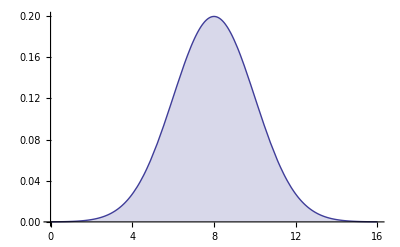

```mathematica
ndist = NormalDistribution[8,2];
Mean[ndist]
Variance[ndist]
StandardDeviation[ndist]
Plot[PDF[ndist,x],{x,0,16}, Filling->Axis]
```

In the cell below, create a Poisson distribution with μ = 5 and name it pdist.  Determine the Mean, the Variance and the StandardDeviation of this distribution.  Explain the results.  Also create a PDF based on this distribution and ListPlot it over the range from 0 to 20.  Can you visually verify the mean and standard deviation from the plot?

5

5

√5

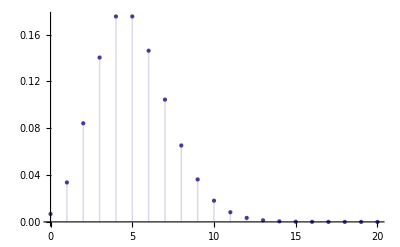

-Graphics-

```mathematica
pdist = PoissonDistribution[5];
Mean[pdist]
Variance[pdist]
StandardDeviation[pdist]
DiscretePlot[PDF[pdist,x],{x,0,20}]
ListPlot[Table[{x,PDF[pdist,x]},{x,0,20}], Filling->Axis]
```

### (#13) Random numbers and statistical sampling (15 min)

It is frequently helpful in both experimental and computational physics to simulate random processes.  For example, you might compare actual data you measure with data generated random variations on some of the parameters.  You could also use random distributions to see how various random variations in your experimental arrangment give different signals.  In computational physics, one often is interested in seeing what the collective properties of a system of random particles or distributions gives under various constraints and conditions.

Browse the basic examples for the first two functions listed there, RandomInteger (discrete) and RandomReal (continuous), both of which sample uniform distibutions (i.e. all values in the specified range are equally probable).  These DC reference pages also have links to several technical tutorials that may be helpful in the future.

(a) In the cell below,  generate a list of 20 pseudorandom integers in the range from -5 to +5, and also generate a list of 20 pseudorandom real numbers in the range from -0.5 to +0.5.

```mathematica
RandomInteger[{-5,5},20]
RandomReal[{-0.5,0.5},20]
```

{-4,-3,2,-3,-2,-3,4,-4,-2,2,-2,-1,-4,1,-5,3,5,-1,4,0}

{0.142296,0.0787263,-0.16816,-0.40875,0.319592,-0.407057,0.1106,-0.260827,0.377163,0.247883,-0.00505241,-0.0583995,0.0676196,-0.396801,-0.0416203,-0.175325,0.0463739,-0.198286,0.337014,-0.14258}

(b) In the cell below, generate a population of 5000 samples from the normal ndist distribution defined in previous exercise (use a semicolon to suppress the output) and name the result nsample.  Compute floating-point values for both the Mean and the StandardDeviation of nsample, and also plot its Histogram.  Note that for our version of Mathematica (8.0), Histogram is part of the Mathematica kernel.  Therefore, the line Needs["Histograms`"] which appears in the first Basic Example is no longer needed.

8.06835

2.00368

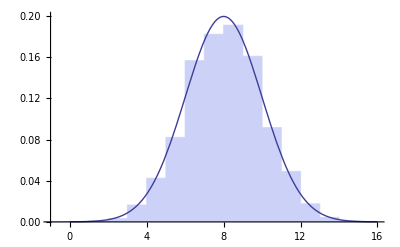

```mathematica
nsample = RandomVariate[ndist,5000];
Mean[nsample]
StandardDeviation[nsample]
Show[Histogram[nsample,20,"PDF"],Plot[PDF[ndist,x],{x,0,16},PlotStyle->Thick]]
```

(c) In the cell below, generate a population of 5000 samples from the Poisson pdist distribution defined in previous exercise (use a semicolon to suppress the output) and name the result psample.  Compute floating-point values for both the Mean and the StandardDeviation of psample, and also plot its Histogram.

5.0086

2.21637

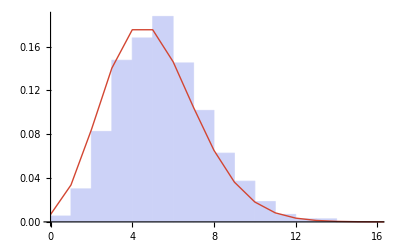

```mathematica
psample = RandomVariate[pdist,5000];
Mean[psample]//N
StandardDeviation[psample]//N
Show[Histogram[psample,200,"PDF"],ListPlot[Table[{x,PDF[pdist,x]},{x,0,20}], Filling->None,Joined->True, ColorFunction->Function[{x,y},Hue[y]]]]
```

### (#14) Adding random variables (10 min)

If one repeats the same physical measurement over and over again, the result will be a little different each time.  We say that such an experiment measures a "random variable", or that it samples a probability distribution.  In the context of experimental measurements, the standard deviation of a random variable is often referred to as "uncertainty" or "error".  Thus, when f is measured to be 7.3 with an uncertainty of 0.5, we write f = 7.3±0.5, which means that σ_f≈0.5 and that μ_f is likely to lie in the range between 6.8 and 7.8.

In the cell below, we create a list called list1 that contains 10^4 samples from a normal distribution with of μ_1 = 20 and σ_1 = 3, and another list called list2 that contains 10^4 samples from a normal distribution with of μ_2 = 30 and σ_2 = 4.  We then add list1 and list2 together to create a list 10^4 sums, and call the result listf.  Finally, we compute the Mean and the StandardDeviation of each of list1, list2 and listf. 

By adding two random variables, p_1 and p_2, with respective means of μ_1 and μ_2 and respective standard deviations of σ_1 and σ_2, we have obtained a third random variable, f=p_1+p_2, with mean μ_f and standard deviation σ_f.  Study the output carefully, and demonstrate for your TA that μ_f = μ_1+μ_2 and σ_f^2=σ_1^2+ σ_2^2.

```mathematica
list1 = Table[ RandomReal[NormalDistribution[20,3]],{10000}];  
list2 =  Table[RandomReal[NormalDistribution[30,4]],{10000}];
listf = list1+list2;

means = Mean/@{list1,list2,listf}
sds =StandardDeviation/@{list1,list2,listf}
```

{20.0468,29.9673,50.0141}

{3.01377,3.96313,4.96674}

```mathematica
Subscript[μ, f] = means[[3]]
Subscript[μ, f2] = means[[1]] + means[[2]]

Subscript[σ, f] = sds[[3]]^2
Subscript[σ, f2] = sds[[1]]^2 + sds[[2]]^2 (*not producing the correct Result... *)
```

50.0141

50.0141

24.6686

24.7893

## Working On Your Own (35 min)

### Adding Waves (10 min)

Write a function to compute the height of a wave h=A cos(k x) where the amplitude A is 1/k.   Then create a function to compute the sum of 5 of these waves with values k=2π, 4π, 6π, 8π, and 10π.  Plot this seond function for values of x between 0 and 5.

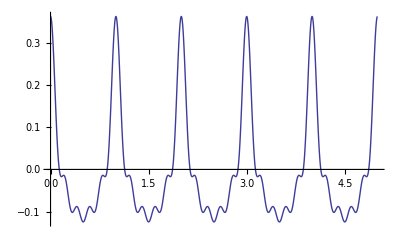

```mathematica
Clear[h]
a = 1/k;
h [k_]= a *Cos[ k*x];
sum = h[2π]+h[4π]+h[6π]+h[8π]+h[10π];(*how could I have wriiten this with a list and placeholders?*)
Plot[sum,{x,0,5}]
```

### Manipulating Data (10 min)

Download the file Th000088.dat into the same directory as this noteboook.  Then read in  the file Th000088.dat, which contains reflectance data from a thin film of thorium taken at the Advanced Light Source at Lawrence Berkeley Labs by executing the following cell.

```mathematica
SetDirectory[NotebookDirectory[]];
tdata = Import["Th000088.dat","Table"];
```

You’ll note that the data contains a header list followed by lists of four numbers.  These represent the wavelength of the beam, the measured reflected signal, and two other numbers which are not needed in this exercise.  Extract the wavelength and signal numbers and plot them using ListLogPlot.

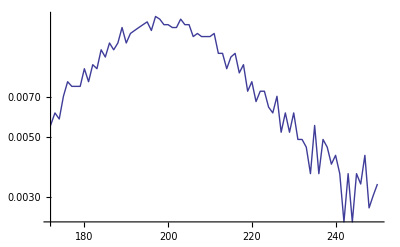

```mathematica
noHeader = Rest[tdata];
{wavelength, signal, other1, other2 } = Transpose[noHeader];
wavelength;
signal;
ListLogPlot[Transpose[{wavelength,signal}],Joined->True]
```

### Statistical Sampling(10 min)

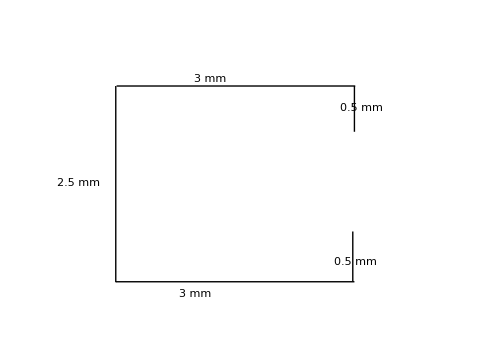
You have a box filled with 10 000 helium atoms with the geometry shown in the following figure.  Each atom is moving in a random direction between -π and π and with a random position in the box.  How many of the atoms make it out of the box without colliding with a wall?
-Graphics-

HINT: A good way to approach this would be to first create a list of random positions and angles for each particle.  Next create a function which will calculuate the angle between the position of a point inside the box and the position of an edge in the slit of the box.  You may find the ArcTan function helpful for this.  Then create a function as Module which takes a list of three elements as an argument ({x_, y_, theta_}) and does three things:

Calculate the angle between the atom position and the top slit

Calculate the angle between the atom and the bottom slit

Return true if the angle of the atom’s trajectory is between the angle to the bottom slit and the top slit.  In other words, if tmax is the angle to the top of the slit and tmin is the angle to the bottom of the slit, the last line in the Module should be  tmin<=theta<=tmax (no semicolon).

Use the Select and Length functions to find how many elements in the list of random atomic locations and directions will make it through the slit without hitting a wall.

```mathematica
xPosition = RandomReal[{0,3},10000];
yPosition = RandomReal[{0,2.5},10000];
theta = RandomReal[{0,2π},10000];
```

```mathematica
dataVectors = Transpose[{xPosition,yPosition,theta}];
```

```mathematica
testFunction[{x_,y_,θ_}]:=Module[{xMax = 3.0, yMin = 0.5, yMax = 2.0},
thetaMax =  ArcTan[(yMax - y)/(xMax-x)];
thetaMin = ArcTan[(y - yMin)/(xMax - x)];
thetaMin<θ < thetaMax]
```

```mathematica
Length[Select[testFunction/@dataVectors ,#==True&]]
```

493